```mathematica
DefPrint["e1453",L[q,q̇]->1/2 Z (q̇)^2-1/2 Subscript[Z, ω] ω^2 q^2-Subscript[Z, λ] λ ω^3 q^4]
```

e1453: L[q,q̇]→(Z (q̇)^2)/2-q^4 λ ω^3 Z_λ-1/2 q^2 ω^2 Z_ω

```mathematica
tmpH=H->Subscript[H, 0]+Subscript[H, 1];
tmpH0=Subscript[H, 0]->1/2 P^2+1/2 ω^2 Q^2;
tmpC=MCommutator[Q,P]==ⅈ;
tmpP=P->D[L[q,q̇],q̇]//HoldOp[D];
tmpP=tmpP/.e1453//ReleaseHold
tmpH=H->P q̇-L[q,q̇]
tmpH=tmpH/.e1453/.tmpP
```

P→Z q̇

H→-L[q,q̇]+P q̇

H→(Z (q̇)^2)/2+q^4 λ ω^3 Z_λ+1/2 q^2 ω^2 Z_ω

Identify q,q̇ with Q, P/Z

```mathematica
tmpP1=tmpP[[2]]/Z->tmpP[[1]]/Z;
tmpHa=tmpH/.tmpP1/.q->Q
```

H→P^2/(2 Z)+Q^4 λ ω^3 Z_λ+1/2 Q^2 ω^2 Z_ω

Subtract H0

```mathematica
tmpHa;
Map[#-Subscript[H, 0]&,%];
%/.Subscript[H, 0]->P^2/2+ω^2 Q^2/2;
%//Collect[#,{P,Q},Simplify]&
tmpH1=H1->%[[2]]
```

H-P^2/2-(Q^2 ω^2)/2→1/2 P^2 (-1+1/Z)+Q^4 λ ω^3 Z_λ+1/2 Q^2 ω^2 (-1+Z_ω)

H1→1/2 P^2 (-1+1/Z)+Q^4 λ ω^3 Z_λ+1/2 Q^2 ω^2 (-1+Z_ω)

```mathematica
tmpH1/.Subscript[Z, λ]->1/.Subscript[Z, ω]->1+B/.Z->1+A//Collect[#,{P,Q},Simplify]&
```

H1→-(A P^2)/(2+2 A)+1/2 B Q^2 ω^2+Q^4 λ ω^3

==============
Rayleigh-Schodinger perturbation technique to define O(λ) corrections to eigenvalues E=E_0+dE, and eigenstates, |Ω>=|0>+d|0>.  Keep only first order in λ.

```mathematica
(*function to keep non-commuting terms in proper order.*)DotForm[a_]:=dotRetain[{H,H0,H1,⟨__|,|__⟩,Sum[_,_],P,Q},a]
```

```mathematica
Print["Define the Hamiltonian as the sum of the pure harmonic oscillator Hamiltonian, H0, and the perturbative Hamiltonian, H1, where λ is the smallness factor",Yield,
subH=H->H0+λ H1,"\nand energy eigenvalues for perturbed and unperturbed states is represented by",Yield,
En[s,j,d],", where s={0,p} for the {unperturbed,perturbed} states and j={0,1,...} indicates energy levels, and d, if present, indicates d-th order expansion in λ." ,"\nThe eigenstates are",Yield,
|{s,j,d}⟩,"\n(The {} is needed because Quantum Notation commutes the BraKet parameters.)"
];

Print["Eigenvalues correction O[λ]-level\n",
"Full equation for level j: ",
tmp=H.|{p,j}⟩->En[p,j]|{p,j}⟩,Imply,
tmp=tmp/.subH;
(*expand in terms of unperturbed quantities.*)
subp={|{p,j_}⟩->|{0,j}⟩+λ|{0,j,1}⟩,En[p,j_]:>En[0,j]+λ En[0,j,1]};
tmp=tmp/.subp//DotForm[#]&;
tmp=tmp/.λ^2->0/.H0.|{0,j_}⟩->En[0,j] |{0,j}⟩;
tmp1=Map[Coefficient[#,λ,0]&,tmp](*zero order term*);
"First order:  ",
tmp1=Map[Coefficient[#,λ,1]&,tmp](*first order term*),Imply,
tmp=Map[⟨{0,j}|.#&,tmp1]//DotForm[#]&;
tmp=tmp/.⟨{0,j}|.H0->En[0,j] ⟨{0,j}|//DotForm[#]&;
tmp=tmp/.⟨a_|.|a_⟩->1;
tmpE11=Apply[Equal,tmp]//Simplify(*first order energy correction.*);
subEj1=tmpE11[[1]]->tmpE11[[2]]
];
```

Define the Hamiltonian as the sum of the pure harmonic oscillator Hamiltonian, H0, and the perturbative Hamiltonian, H1, where λ is the smallness factor
→ H→H0+H1 λ
and energy eigenvalues for perturbed and unperturbed states is represented by
→ En[s,j,d], where s={0,p} for the {unperturbed,perturbed} states and j={0,1,...} indicates energy levels, and d, if present, indicates d-th order expansion in λ.
The eigenstates are
→ |{s,j,d}⟩
(The {} is needed because Quantum Notation commutes the BraKet parameters.)

Eigenvalues correction O[λ]-level
Full equation for level j: H.|{p,j}⟩→En[p,j] |{p,j}⟩
⇒ First order:  H0.|{0,j,1}⟩+H1.|{0,j}⟩→En[0,j,1] |{0,j}⟩+En[0,j] |{0,j,1}⟩
⇒ ⟨{0,j}|.H1.|{0,j}⟩→En[0,j,1]

```mathematica
Print["Assume unit[n] is a decomposition of unity where |{0,n}⟩ is singled out and orthogonal to all other vectors.",
unit[n_]:=Sum[|{0,k}⟩.⟨{0,k}|,{k,k≠n}]+|{0,n}⟩.⟨{0,n}|;
"For example, ",
unit[1]
];
```

Assume unit[n] is a decomposition of unity where |{0,n}⟩ is singled out and orthogonal to all other vectors.For example, |{0,1}⟩.⟨{0,1}|+∑_k^(k≠1) |{0,k}⟩.⟨{0,k}|

Compute purturbed eigenstates--Decompose first order equation into eigenstates

```mathematica
Print["Compute perturbed Hamiltonian on |{0,j}⟩: ",Yield,
tmp=H1.|{0,j}⟩==unit[j].H1.|{0,j}⟩;Yield;
(*apply above expression for E1.*)
tmp1a=tmp/.subEj1//DotForm[#]&;
(*subtract O(λ) H equation*)
tmp=tmp1a[[1]]-tmp1[[1]]==tmp1a[[2]]-tmp1[[2]];Yield;
(*assume non-degenerate states, apply unperturbed eigenstates <k|*)
tmp=Map[⟨{0,k}|.#&,tmp]/.⟨{0,k}|.Sum[_,_]->⟨{0,k}|//DotForm[#]&;Yield;
tmp=tmp/.⟨{0,k}|.H0->En[0,k] ⟨{0,k}|//DotForm[#]&;Yield;
tmp=tmp/.⟨{0,k}|.|{0,j}⟩->0;(*eigenstates non-degenerate*)
sub=Solve[tmp,⟨{0,k}|.|{0,j,1}⟩][[1]];Yield;
tmp=|{0,j,1}⟩==unit[j].|{0,j,1}⟩(*spectral decompose*);
tmp=tmp/.Sum[a_,b_].|{0,j,1}⟩->Sum[a.|{0,j,1}⟩,b]/.sub;Yield;
tmpeigen=tmp/.⟨{0,j}|.|{0,j,1}⟩->0(*assume orthogonal.*)
];
```

Compute perturbed Hamiltonian on |{0,j}⟩: 
→ |{0,j,1}⟩==∑_k^(k≠j) |{0,k}⟩.⟨{0,k}|.H1.|{0,j}⟩/(En[0,j]-En[0,k])

Define Q,P operations on eigenvectors.

```mathematica
subQP={Q->(a+SuperDagger[a])/√(2 ω),P->ⅈ √(ω/2)(SuperDagger[a]-a),a.|{s_,n_}⟩:>√n|{s,n-1}⟩,SuperDagger[a].|{s_,n_}⟩:>√(n+1)|{s,n+1}⟩,⟨a_|.|a_⟩->1,⟨a_|.|b_⟩:>KroneckerDelta[a,b]};
OpQP[exp_]:=Module[{tmp=exp,tmpl=0},
While[tmpl=!=tmp,tmpl=tmp; tmp=tmp//.subQP;tmp=dotRetain[{a,SuperDagger[a],|_⟩,⟨_|},tmp]];
tmpl];
Print["With these definitions:\n",
tmp=(Q.P-P.Q).|{0,j}⟩;tmp->OpQP[tmp],"\n",
tmp=Q.|{0,0}⟩;tmp->OpQP[tmp],"\n",
tmp=P.|{0,0}⟩;tmp->OpQP[tmp],"\n",
tmp=⟨{0,0}|.P.P.|{0,0}⟩;tmp->OpQP[tmp]
];
```

With these definitions:
(-P.Q).|{0,j}⟩+Q.P.|{0,j}⟩→ⅈ |{0,j}⟩
Q.|{0,0}⟩→(|{0,1}⟩)/(√2 √ω)
P.|{0,0}⟩→(ⅈ √ω |{0,1}⟩)/(√2)
⟨{0,0}|.P.P.|{0,0}⟩→ω/2

The eigenvalue correction for each unperturbed eigenvalue for the provided conditions

```mathematica
Print["The perturbation to the unperturbed energy states:\n",
tmp=subEj1/.tmpH1/.Subscript[Z, ω]->1+B/.Subscript[Z, λ]->1/.Z->1+A/.P^n_:>DotPower[P,n]/.Q^n_:>DotPower[Q,n],Yield,
tmp=tmp//DotForm[#]&;Yield;
tmp=OpQP[tmp];Yield;
"\nThen to O(λ) with the substitutions: ",sub={A->Subscript[κ, A] λ,B->Subscript[κ, B] λ}," the perturbation for the j-th level becomes",Imply,
perturbEigenvalueJ=Series[tmp[[1]]/.sub,{λ,0,1}]//Normal//Simplify,
"\nFor example j=0: ",
perturbEigenvalueJ/.j->0
];
```

The perturbation to the unperturbed energy states:
⟨{0,j}|.(1/2 (-1+1/(1+A)) P.P).|{0,j}⟩+⟨{0,j}|.(1/2 B ω^2 Q.Q).|{0,j}⟩+⟨{0,j}|.(λ ω^3 Q.Q.Q.Q).|{0,j}⟩→En[0,j,1]
→ 
Then to O(λ) with the substitutions: {A→λ κ_A,B→λ κ_B} the perturbation for the j-th level becomes
⇒ 1/4 λ ω (3+6 j+6 j^2-(1+2 j) κ_A+(1+2 j) κ_B)
For example j=0: 1/4 λ ω (3-κ_A+κ_B)

The eigenvector correction with the above perturbation.

```mathematica
Print[tmp=tmpeigen,Imply,
tmp=tmp/.tmpH1/.Subscript[Z, ω]->1+B/.Subscript[Z, λ]->1/.Z->1+A/.P^n_:>DotPower[P,n]/.Q^n_:>DotPower[Q,n],Imply;
tmp=tmp//DotForm[#]&;Yield;
tmp=OpQP[tmp];Yield;
tmp=tmp/.KroneckerDelta[{0,j},{0,k}]->0;
tmp=tmp/.KroneckerDelta[{0,a_},{0,b_}]->KroneckerDelta[a,b];
tmp=tmp/.KroneckerDelta[j,k]->0;
tmp=tmp//SumKronecker;Yield;
tmp=tmp/.Sum[a_,b_]->a;Yield;
"\nThen to O(λ) with the substitutions: ",sub={A->Subscript[κ, A] λ,B->Subscript[κ, B] λ},Yield,
tmp=tmp/.sub;
perturbEigenvector=Series[tmp,{λ,0,1}]//Normal//Simplify
];
```

|{0,j,1}⟩==∑_k^(k≠j) |{0,k}⟩.⟨{0,k}|.H1.|{0,j}⟩/(En[0,j]-En[0,k])
⇒ |{0,j,1}⟩==∑_k^(k≠j) |{0,k}⟩.1/(En[0,j]-En[0,k])(⟨{0,k}|.(1/2 (-1+1/(1+A)) P.P).|{0,j}⟩+⟨{0,k}|.(1/2 B ω^2 Q.Q).|{0,j}⟩+⟨{0,k}|.(λ ω^3 Q.Q.Q.Q).|{0,j}⟩)
Then to O(λ) with the substitutions: {A→λ κ_A,B→λ κ_B}
→ |{0,j,1}⟩==1/4 λ ω ((√(-3+j) √(-2+j) √(-1+j) √j |{0,-4+j}⟩)/(-En[0,-4+j]+En[0,j])-(√(-1+j) √j (-2+4 j+κ_A+κ_B) |{0,-2+j}⟩)/(En[0,-2+j]-En[0,j])+√(1+j) √(2+j) (((6+4 j+κ_A+κ_B) |{0,2+j}⟩)/(En[0,j]-En[0,2+j])+(√(3+j) √(4+j) |{0,4+j}⟩)/(En[0,j]-En[0,4+j])))

Evaluate the ground and first excited states of the full system where En[0,1]-En[0,0]=ω

```mathematica
(*perturbative eigenvalue function*)
En[0,k_,1]:=perturbEigenvalueJ/.j->k;
Print["The defined excitation energy, ω, ",Yield,
tmp=0==En[0,1,1]-En[0,0,1]//Simplify,Yield,
eq1=Solve[tmp,Subscript[κ, A]][[1]]/.Rule->Equal
];
```

The defined excitation energy, ω, 
→ λ ω (-6+κ_A-κ_B)==0
→ {κ_A==6+κ_B}

```mathematica
(*perturbative eigenvector function*)eigenVector[k_]:=perturbEigenvector/.j->k;
subV[k_]:=|{p,k}⟩->|{0,k}⟩+eigenVector[k][[2]];
subVt[k_]:=subV[k]/.|a__⟩->⟨a|;
Print["The suggested normalization",Yield,
tmp=1/√(2 ω)==⟨{p,1}|.Q.|{p,0}⟩,Yield,
tmp=tmp/.subVt[1]/.subV[0];Yield;
tmp=OpQP[tmp]/.λ^2->0//Simplify,Yield,
eq2=Solve[tmp,Subscript[κ, A]][[1]]/.Rule->Equal
];
```

The suggested normalization
→ 1/(√2 √ω)==⟨{p,1}|.Q.|{p,0}⟩
→ (λ √ω (6+κ_A+κ_B))/(En[0,0]-En[0,2])==0
→ {κ_A==-6-κ_B}

```mathematica
Solve[Flatten[{eq1,eq2}],{Subscript[κ, A],Subscript[κ, B]}]
```

{{κ_A→0,κ_B→-6}}

VVVVVV
Propagator to O[λ] in dimension->1

Analogous with (14.4) where the perturbation term,Π, is derived from the 4 particle interaction term and where {A→-1+Z,B→-1+Z_m} and the coefficient is lumped λ ω^3 Z_λ→λ

a144: ⅈ Π[k_]→-ⅈ (A k^2+B m^2)-1/2 ⅈ λ^2 IntegralOp[{{h1},{h2}},Δ[h1] Δ[h2] Δ[h1+h2+k]]

The diagram of this interaction looks like:

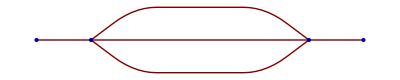

Using (14.3), the free particle propagator,

e143: Δ[k_]→1/(k^2+m^2-ⅈ ϵ)

⇒ ⅈ Π[k_]→-ⅈ (A k^2+B m^2)-1/2 ⅈ λ^2 IntegralOp[{{h1},{h2}},1/((h1^2+m^2-ⅈ ϵ) (h2^2+m^2-ⅈ ϵ) ((h1+h2+k)^2+m^2-ⅈ ϵ))]
⇒ ⅈ Π[k_]→-ⅈ (A k^2+B m^2)-1/2 ⅈ λ^2 xIntegrate[1/((h1^2+m^2-ⅈ ϵ) (h2^2+m^2-ⅈ ϵ) ((h1+h2+k)^2+m^2-ⅈ ϵ)),h1,h2]
Or with Feymann's formula
→ ⅈ Π[k_]→-ⅈ (A k^2+B m^2)-1/2 ⅈ λ^2 IntegralOp[{{h1},{h2},{x1},{x2},{x3}},(2 DiracDelta[-1+x1+x2+x3])/((x1 (h1^2+m^2-ⅈ ϵ)+x2 (h2^2+m^2-ⅈ ϵ)+x3 ((h1+h2+k)^2+m^2-ⅈ ϵ))^3)]

and the  conditions {Π[-m^2]→0,Π'[-m^2]→0} to set the values of A and B.

```mathematica
Print["Analogous with (14.4) where the perturbation term,Π, is derived from the 4 particle interaction term and where ",subAB={A->Z-1,B->Subscript[Z, m]-1}," and the coefficient is lumped ",Subscript[Z, λ] λ ω^3->λ];
DefPrint["a144",ⅈ Π[k_]->1/2(ⅈ λ)^2(-ⅈ)^3 IntegralOp[{{h1},{h2}},Δ[(h1)]Δ[(h1+h2+k)]Δ[h2]]
-ⅈ(A k^2+B m^2)];
Print["The diagram of this interaction looks like:"
];
GraphPlot[{1->2,2->3,2->3,2->3,3->4},VertexCoordinateRules->{1->{.08,0},2->{.1,0},3->{.18,0},4->{.2,0}}]

Print["Using (14.3), the free particle propagator,"];
DefPrint["e143",Δ[k_]->1/(k^2+m^2-ⅈ ϵ)];
Print[Imply,
tmp1=tmp=a144/.e143,Imply,
tmp1=tmp1/.IntegralOp[a_List,b_]:>xIntegrate[b,Flatten[a][[1]],Flatten[a][[2]]],
"\nOr with Feymann's formula",Yield,
tmp=tmp/.IntegralOp[a__List,1/(b_ c_ d_)]:>IntegralOp[Partition[Flatten[{a,{x1},{x2},{x3}}],1],2 DiracDelta[x1+x2+x3-1](x1 b+x2 c +x3 d)^-3]
];

Print["and the  conditions ",{Π[-m^2]->0,Π'[-m^2]->0}," to set the values of A and B."
];
```

```mathematica
Print["Use Cauchy Residue Theorem for integration:\n",
tmp1;Yield;
tmp=Extract[tmp1,Position[tmp1,xIntegrate[___]]][[1]],
"For the h1 integration there are 4 potential poles to be selected by the contours of {h1,h2} to be in part along the x-axis and the portion around the upper half-circle equal to 0.",Yield,
tmpn=tmp/.xIntegrate[a_,b_,c_]:>Denominator[a];Yield;
pole=Solve[tmpn==0,h1],
"\nOf these poles h1={2,4} are only in the upper-half plane since {k,h2}∈Reals."];
```

Use Cauchy Residue Theorem for integration:
xIntegrate[1/((h1^2+m^2-ⅈ ϵ) (h2^2+m^2-ⅈ ϵ) ((h1+h2+k)^2+m^2-ⅈ ϵ)),h1,h2]For the h1 integration there are 4 potential poles to be selected by the contours of {h1,h2} to be in part along the x-axis and the portion around the upper half-circle equal to 0.
→ {{h1→-h2-k-√(-m^2+ⅈ ϵ)},{h1→-h2-k+√(-m^2+ⅈ ϵ)},{h1→-√(-m^2+ⅈ ϵ)},{h1→√(-m^2+ⅈ ϵ)}}
Of these poles h1={2,4} are only in the upper-half plane since {k,h2}∈Reals.

```mathematica
ip=4;
Print["Investigate the h1 Residue at pole[",ip,"],
in the upper half plane: ",pole[[ip,1]],Yield,
res[ip]=tmp/.xIntegrate[a_,b_,c_]:>Residue[a,{pole[[ip,1,1]],pole[[ip,1,2]]}],Yield,
"The pole structure of h2 at h1 pole[",ip,"]:",
pole2=Solve[Denominator[res[ip]]==0,h2],
"\nOf these h2 poles {4} is the only one in the upper-half plane (assuming {k}∈Reals)",
ip2=4;
"\nSo the residue at ",pole2[[ip2,1]],Yield,
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}],Yield,
"So the {h1,h2}->{4,4} residue ",Yield,
res2[ip,ip2] /.ϵ->0//Simplify];
```

Investigate the h1 Residue at pole[4],
in the upper half plane: h1→√(-m^2+ⅈ ϵ)
→ 1/(2 (h2+k) (h2+k+2 √(-m^2+ⅈ ϵ)) (h2^2+m^2-ⅈ ϵ) √(-m^2+ⅈ ϵ))
→ The pole structure of h2 at h1 pole[4]:{{h2→-k},{h2→-k-2 √(-m^2+ⅈ ϵ)},{h2→-√(-m^2+ⅈ ϵ)},{h2→√(-m^2+ⅈ ϵ)}}
Of these h2 poles {4} is the only one in the upper-half plane (assuming {k}∈Reals)
So the residue at h2→√(-m^2+ⅈ ϵ)
→ -1/(4 (k+√(-m^2+ⅈ ϵ)) (k+3 √(-m^2+ⅈ ϵ)) (m^2-ⅈ ϵ))
→ So the {h1,h2}->{4,4} residue 
→ -1/(4 m^2 (k^2-3 m^2+4 k √(-m^2)))

```mathematica
ip=2;
Print["Investigate the h1 Residue at pole[",ip,"], 
in the upper half plane: ",pole[[ip,1]],Yield,
res[ip]=tmp/.xIntegrate[a_,b_,c_]:>Residue[a,{pole[[ip,1,1]],pole[[ip,1,2]]}],Yield,
"The pole structure of h2 at h1 pole[",ip,"]:",
pole2=Solve[Denominator[res[ip]]==0,h2],

"\nOf these h2 poles {2,4} are in the upper-half plane (assuming {k}∈Reals)",
ip2=2;
"\nSo the residue at ";pole2[[ip2,1]];Yield;
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}];
"\nThe {h1,h2}->{",ip,",",ip2,"} residue ",Yield,
res2[ip,ip2] /.ϵ->0//Simplify,
ip2=4;
"\nThe residue at ";pole2[[ip2,1]];Yield;
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}];
"\nThe {h1,h2}->{",ip,",",ip2,"} residue ",Yield,
res2[ip,ip2] /.ϵ->0//Simplify
];
```

Investigate the h1 Residue at pole[2], 
in the upper half plane: h1→-h2-k+√(-m^2+ⅈ ϵ)
→ -1/(2 (h2+k) (-h2-k+2 √(-m^2+ⅈ ϵ)) (h2^2+m^2-ⅈ ϵ) √(-m^2+ⅈ ϵ))
→ The pole structure of h2 at h1 pole[2]:{{h2→-k},{h2→-k+2 √(-m^2+ⅈ ϵ)},{h2→-√(-m^2+ⅈ ϵ)},{h2→√(-m^2+ⅈ ϵ)}}
Of these h2 poles {2,4} are in the upper-half plane (assuming {k}∈Reals)
The {h1,h2}->{2,2} residue 
→ 1/(4 m^2 (-k^2+3 m^2+4 k √(-m^2)))
The {h1,h2}->{2,4} residue 
→ -1/(4 m^2 (k^2+m^2))

```mathematica
Print["The sum of the residues, res2[4,4]+res2[2,2]+res2[2,4]",Yield,
resSum=res2[4,4]+res2[2,2]+res2[2,4]/.ϵ->0//FullSimplify
];
```

The sum of the residues, res2[4,4]+res2[2,2]+res2[2,4]
→ -3/(4 k^2 m^2+36 m^4)

```mathematica
ip2=1;ip=2;
Print["Does the pole at ",pole2[[ip2,1]]," contribute?"]
Print["The residue at {h1,h2}->{",ip,",",ip2,"} = ",
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}]
];
ip=4;
Print["The residue at {h1,h2}->{",ip,",",ip2,"} = ",
res2[ip,ip2]=Residue[res[ip],{pole2[[ip2,1,1]],pole2[[ip2,1,2]]}]
];
Print["Showing cancellation."];
```

Does the pole at h2→-k contribute?

The residue at {h1,h2}->{2,1} = 1/(4 (m^2-ⅈ ϵ) (k^2+m^2-ⅈ ϵ))

The residue at {h1,h2}->{4,1} = -1/(4 (m^2-ⅈ ϵ) (k^2+m^2-ⅈ ϵ))

Showing cancellation.